# Laplace Eqn. and Diffusion Eqn.

#### Author

R.M. Jones, 10 - 2021.

#### Options (exec these to setup base features)

```mathematica
fntSize=14;

SetOptions[#,BaseStyle->{FontSize->fntSize,FontWeight->Bold,FontFamily->"Helvetica",FontColor->RGBColor[0,0,0]},Frame->True]&/@{ArrayPlot,Plot,ListPlot,Plot3D,ListLinePlot,BarChart,Histogram,ContourPlot,ContourPlot3D,
ListDensityPlot};

SetOptions[Plot3D,BaseStyle->{FontSize->fntSize,FontWeight->Bold,FontFamily->"Helvetica",FontColor->RGBColor[0,0,0]}];

SetOptions[Graphics3D,BaseStyle->{FontSize->fntSize,FontWeight->Bold,FontFamily->"Helvetica",FontColor->RGBColor[0,0,0]}];
```

## Laplace Equation: Electrostatic Field in a Box

#### Cube Graphics

```mathematica
hues=Join[Hue[1]&/@Range[2],{Hue[1,1,0.]},Hue[1]&/@Range[3]];

v={{0,0,0},{1,0,0},{1,1,0},{0,1,0},{0,0,1},{1,0,1},{1,1,1},{0,1,1}};

idx={{1,2,3,4},{1,2,6,5},{2,3,7,6},{3,4,8,7},{4,1,5,8},{5,6,7,8}};
pt=Show[Graphics3D[Table[{Glow@hues[[i]],Polygon[v[[idx[[i]]]]]},{i,6}],Lighting->None,Axes->False,Ticks->False,Boxed->False,
AxesLabel->{"x","y","z"},ImageSize->{200,200}
],Graphics3D[{Text["L",{1.05,-.1,0}],
Text["L",{0.3,0.5,1.4}],
Text["0",{0.,0.,-.175}],
Text["x",{.5,-.17,0}],
Text["y",{-.125,.55,1}]
},
Boxed->False],ImageSize->{150,150}]


SetDirectory["/Users/rmj/Dropbox (The University of Manchester)/Undergraduates & Term Activities/Courses Taught/PHYS20171/RMJ Lectures/Laplace and Diffusion Equation/Pics"];
Export["laplacecube.png",pt]
```

```mathematica
pt=-Graphics3D-;SetDirectory["/Users/rmj/Dropbox (The University of Manchester)/Undergraduates & Term Activities/Courses Taught/PHYS20171/RMJ Lectures/Laplace and Diffusion Equation/Pics"];
Export["laplacecube.png",pt]
```

laplacecube.png

#### Box Graphics 1

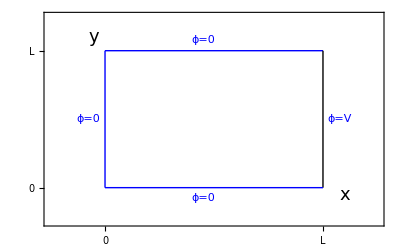

```mathematica
ms[x_]:=StyleForm[x,FontSize->18,FontWeight->"Heavy"];

pbox=Plot[1,{x,0,1},
PlotStyle->{Blue,Thick},AxesStyle->Arrowheads[{0.05}],

FrameTicks->{{{{0,0},{1,"L"}},None},{{{0,0},{1,"L"}},None}},

FrameStyle->Opacity[0],
Epilog->{Thick,Line[{{1,0},{1,1}}],Blue,
Line[{{0,0},{0,1}}],Line[{{0,0},{1,0}}],
Text["ϕ=V",{1.075,.5}],
Text["ϕ=0",{-.075,.5}],
Text["ϕ=0",{.45,1.075}],
Text["ϕ=0",{.45,-.075}],
Black,Text[ms["y"],{-.05,1.1}],
Text[ms["x"],{1.1,-.05}]
},
PlotRange->{{-.25,1.25},{-.25,1.25}}
]
```

```mathematica
pboxnew=ImageTrim[pbox,{{100,100},{1200,1200}}]
```

-Graphics-

```mathematica
SetDirectory["/Users/rmj/Dropbox (The University of Manchester)/Undergraduates & Term Activities/Courses Taught/PHYS20171/RMJ Lectures/Laplace and Diffusion Equation/Pics"];
Export["laplacebox.png",pboxnew]
```

laplacebox.png

```mathematica
Graphs
```

```mathematica
ms[x_]:=StyleForm[x,FontSize->18,FontWeight->"Heavy"];
```

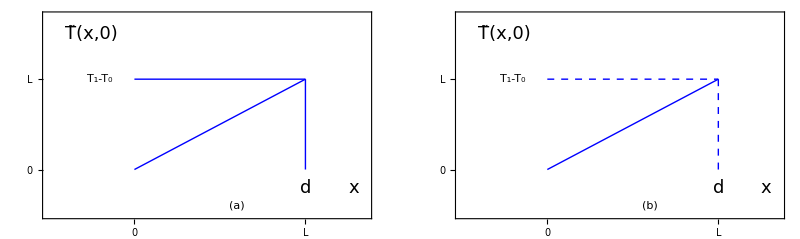

```mathematica
pinit=Show[GraphicsArray[{
Plot[x,{x,0,1},
PlotStyle->{Blue,Thick},AxesStyle->Arrowheads[{0.05}],
FrameTicks->{{{{0,0},{1,"L"}},None},{{{0,0},{1,"L"}},None}},
FrameStyle->Opacity[0],
Epilog->{Thick,Blue,Line[{{1,0},{1,1}}],
Thin,Line[{{0,1},{1,1}}],
Black,Text[ms["T̃(x,0)"],{-.25,1.5}],
Text["T_1-T_0",{-.2,1}],
Text[ms["x"],{1.28,-.2}],
Text[ms["d"],{1,-.2}],
Text["(a)",{.6,-.4}]
},
PlotRange->{{-.5,1.35},{-.5,1.7}}
],
Plot[x,{x,0,1},
PlotStyle->{Blue,Thick},AxesStyle->Arrowheads[{0.05}],
FrameTicks->{{{{0,0},{1,"L"}},None},{{{0,0},{1,"L"}},None}},
FrameStyle->Opacity[0],
Epilog->{Thin,Blue,Dashed,Line[{{1,0},{1,1}}],
Thick,
Thin,Line[{{0,1},{1,1}}],
Black,Text[ms["T̃(x,0)"],{-.25,1.5}],
Text["T_1-T_0",{-.2,1}],
Text[ms["x"],{1.28,-.2}],
Text[ms["d"],{1,-.2}],
Text["(b)",{.6,-.4}]
},
PlotRange->{{-.5,1.35},{-.5,1.7}}
]


}]]
```

```mathematica
pinitnew=ImageTrim[pinit,{{100,100},{1800,1800}}]
```

-Graphics-

```mathematica
SetDirectory["/Users/rmj/Dropbox (The University of Manchester)/Undergraduates & Term Activities/Courses Taught/PHYS20171/RMJ Lectures/Laplace and Diffusion Equation/Pics"];
Export["initconditions.png",pinitnew]
```

initconditions.png

#### Box Graphics 2

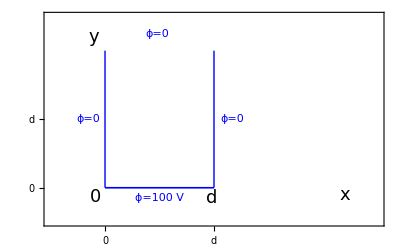

```mathematica
ms[x_]:=StyleForm[x,FontSize->18,FontWeight->"Heavy"];

pbox=Plot[0,{x,0,.5},
PlotStyle->{Blue,Thick},AxesStyle->Arrowheads[{0.05}],

FrameTicks->{{{{0,0},{.5,"d"}},None},{{{0,0},{.5,"d"}},None}},

FrameStyle->Opacity[0],
Epilog->{Blue,Thick,Line[{{.5,0},{.5,1}}],Blue,
Line[{{0,0},{0,1}}],Line[{{0,0},{.5,0}}],
Text["ϕ=0",{.585,.5}],
Text["ϕ=0",{-.075,.5}],
Text["ϕ=0",{.24,1.12}],

Text["ϕ=100 V",{.25,-.075}],
Black,
Text[ms["d"],{.49,-.075}],Text[ms["0"],{-.045,-.065}],
Text[ms["y"],{-.05,1.1}],
Text[ms["x"],{1.1,-.05}]
},
PlotRange->{{-.25,1.25},{-.25,1.25}}
]
```

```mathematica
pboxnew=ImageTrim[pbox,{{100,100},{1200,1200}}]
```

-Graphics-

```mathematica
SetDirectory["/Users/rmj/Dropbox (The University of Manchester)/Undergraduates & Term Activities/Courses Taught/PHYS20171/RMJ Lectures/Laplace and Diffusion Equation/Pics"];
Export["laplaceboxStack.png",pboxnew]
```

laplaceboxStack.png

```mathematica
Graphs
```

```mathematica
ms[x_]:=StyleForm[x,FontSize->18,FontWeight->"Heavy"];
```

```mathematica
pinit=Show[GraphicsArray[{
Plot[x,{x,0,1},
PlotStyle->{Blue,Thick},AxesStyle->Arrowheads[{0.05}],
FrameTicks->{{{{0,0},{1,"L"}},None},{{{0,0},{1,"L"}},None}},
FrameStyle->Opacity[0],
Epilog->{Thick,Blue,Line[{{1,0},{1,1}}],
Thin,Line[{{0,1},{1,1}}],
Black,Text[ms["T̃(x,0)"],{-.25,1.5}],
Text["T_1-T_0",{-.2,1}],
Text[ms["x"],{1.28,-.2}],
Text[ms["d"],{1,-.2}],
Text["(a)",{.6,-.4}]
},
PlotRange->{{-.5,1.35},{-.5,1.7}}
],
Plot[x,{x,0,1},
PlotStyle->{Blue,Thick},AxesStyle->Arrowheads[{0.05}],
FrameTicks->{{{{0,0},{1,"L"}},None},{{{0,0},{1,"L"}},None}},
FrameStyle->Opacity[0],
Epilog->{Thin,Blue,Dashed,Line[{{1,0},{1,1}}],
Thick,
Thin,Line[{{0,1},{1,1}}],
Black,Text[ms["T̃(x,0)"],{-.25,1.5}],
Text["T_1-T_0",{-.2,1}],
Text[ms["x"],{1.28,-.2}],
Text[ms["d"],{1,-.2}],
Text["(b)",{.6,-.4}]
},
PlotRange->{{-.5,1.35},{-.5,1.7}}
]


}]]
```

-Graphics-

```mathematica
pinitnew=ImageTrim[pinit,{{100,100},{1800,1800}}]
```

-Graphics-

```mathematica
SetDirectory["/Users/rmj/Dropbox (The University of Manchester)/Undergraduates & Term Activities/Courses Taught/PHYS20171/RMJ Lectures/Laplace and Diffusion Equation/Pics"];
Export["initconditions.png",pinitnew]
```

initconditions.png

#### Main (Start here!)

Laplace Equation:

∇^2 ϕ=0

This is the function we will use to solve the 2-D square boundary (see notes) -- you will need to  execute the below (shift-enter together).

Also, recall the boundary conditions: ϕ(x,0)=ϕ(x,L)=ϕ(0,y)=0 and ϕ(L,y)=V.

```mathematica
Clear[phi];phi[x_,y_,ntot_:10,L_:1]:=4./π Sum[1/(n Sinh[n π]) Sinh[ (n π x)/L] Sin[ (n π y)/L],{n,1,ntot,2}]
```

Try using is yourself!

```mathematica
phi[1,.9]
```

1.18233

Is it zero along y = 0? Try the below (and swap also try phi[#,1])

```mathematica
{#,phi[#,0]}&/@Range[0,1,.1]
```

{{0.,0.},{0.1,0.},{0.2,0.},{0.3,0.},{0.4,0.},{0.5,0.},{0.6,0.},{0.7,0.},{0.8,0.},{0.9,0.},{1.,0.}}

Here is a 3 - D plot of the function ϕ (x, y)  -- try varying the number of terms (and keep in mind the boundary conditions).

```mathematica
Manipulate[Plot3D[phi[x,y,ntotal],{x,0,1},{y,0,1},AxesLabel->{"x (L)","y (L)","ϕ (V)"},PlotPoints->50,PlotRange->All,AxesStyle->Arrowheads[{0.05}],
ImageSize->size
],
{{ntotal,1,StyleForm["# of terms",FontWeight->Bold,FontSize->18]},1,80,2,Appearance->"Labeled"},
{{size,Medium,"Size"},{Medium,Large}},
SaveDefinitions->True]
```

A contour plot might be easier to see the behaviour (your choice!)

```mathematica
Manipulate[ContourPlot[phi[x,y,ntotal],{x,0,1},{y,0,1},Contours->20,PlotLegends->Automatic,
ImageSize->size,

FrameLabel->{"x","y"},PlotPoints->100],{{ntotal,1,StyleForm["# of terms",FontWeight->Bold,FontSize->18]},1,80,1,Appearance->"Labeled"},
{{size,Medium,"Size"},{Medium,Large}}
]
```

Finally, let us take a look at the value of ϕ on the boundary x=L, i.e. ϕ (L, y) -- here you should try varying the number of terms by moving the slider (not only odd terms will automatically be added in the summation).

It should converge to 1 (in units of V)  -- clearly one term is  not sufficient.    

There is also clearly a Gibbs phenomena evident here too (refer to notes on Fourier series).

```mathematica
Manipulate[Plot[Evaluate[phi[1,y,#]&/@Range[1,nn,10]],{y,0,1},
Epilog->{Red,Dashing[.01],Line[{{0,1},{1,1}}]},
PlotRange->All],{{nn,1,StyleForm["# of Terms",FontWeight->Bold,FontSize->18]},1,80,10,Appearance->"Labeled"},Initialization:>(phi[x_,y_,ntot_:10,L_:1]:=4./π Sum[1/(n Sinh[n π]) Sinh[ (n π x)/L] Sin[ (n π y)/L],{n,1,ntot,2}])]
```

## Diffusion/Heat Equation: Heat flow through an infinite slab

∇^2 T=1/α^2(∂T)/(∂t)

Here we will investigate the solution to the heat - flow equation studied in the lectures, i.e. a slab is initially in steady state with its two faces held at different temperatures when suddenly one face has its temperature changed. 

How does the temperature vary subsequently?

#### Main

```mathematica
Clear[fun,x,t,nf,a,d];fun[x_,t_,nf_:10,a_:1,d_:1]:=2/π Sum[1/n (-1)^(n+1)Exp[-(n  π a/d)^2 t]  Sin[(n π x)/d],{n,1,nf}]
```

Compare this with your notes  (but also try varying the number of terms!)....

```mathematica
Manipulate[Grid[Join[{{"n","T(x,n)"}},Table[{i,fun[x,t,i,α,d]},{i,1,terms}]],Frame->All],{{terms,1,"# of Terms"},1,20,1,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
fun[.999,0,100000,1,1]
```

0.996974

```mathematica
Manipulate[Animate[Plot[fun[x,t,nn],{x,0,1},PlotRange->{Automatic,{-.1,2}},
PlotStyle->{Thick,Red},

FrameTicks->{{{{0,0}},None},{{{0,0},{1,1}},None}},Epilog->{Dashed,Line[{{0,1},{1,1}}]},
FrameLabel->{"x (d)","T̃(x,t)"},
ImageSize->size],
{t,0,.4,.00000001},
AnimationRunning->False,AnimationRate->.005],{{size,Medium,"Size"},{Medium,Large}},{{nn,4,StyleForm["# of terms",FontWeight->Bold,FontSize->18]},1,100,1,Appearance->"Labeled"},SaveDefinitions->True
]
```

In the notes recall we have T̃=T_0+  2/π (T_1-T_0) ∑_(n=1)^∞ (-1)^(n+1)/n e^(-((α n π)/d)^2 t) sin (n π x/d) .  
Thus for t=0 and x=d for example we need,
  2/π∑_(n=1)^∞ (-1)^(n+1)/n e^(-((α n π)/d)^2 t) sin (n π x/d) = 1 -- Verify this is the case and also note the Gibbs phenoma!

```mathematica
txt=  2/π∑_(n=1)^∞ (-1)^(n+1)/n e^(-((α n π)/d)^2 t) sin (n π x/d);
```

```mathematica
Manipulate[fun[.999,0,n,1,1],{n,1,100000,1}]
```

Other interesting features to note!

1. For t=0 the initial temperature distribution should be linear -- is it?

2. For t=0 do you see a Gibbs phenomena (vary the number of terms to confirm)?

3. As time progresses which eigenmodes (in the summation) start to dominate? 

4. As t → ∞ then all modes damp down of course and the temperature goes to zero (remember the shifting property) and this is effectively T̃.

```mathematica
txt=ToExpression["\\tilde{T}(x,t)=\\frac{2}{\\pi} \\sum_ {n=1}^{\\infty}\\frac {(-1)^{n+1}} {n} e^{-(\\alpha n\\pi/d)^2 t}\\sin \\left( \\frac{ n \\pi x} {d} \\right)",TeXForm,HoldForm];

Off[General::munfl];
res=ListAnimate[Table[Plot[fun[x,t/100,100],{x,0,1},
PlotStyle->{Thick,Red},
Epilog->{Dashed,Line[{{0,1},{1,1}}],
Text[txt,{.4,.8}]},
AxesLabel->{"x/d","T̃(x,t)"},
PlotLabel->"Fridge T̃(x,t)",ImageSize->Large,
PlotRange->{Automatic,{-.1,1.2}},FrameLabel->True],{t,0,10}]]
```